The Oregonator: numerical integration
Collegio Superiore dell’Università di Bologna, A.A. 2020-2021
          Seminario “The Compartmental Models: from Ecological Systems to Epidemic
             Spreading”

We attempt an explicit implementation of the Runge-Kutta 4th order integrator in order to approximate solutions to the Oregonator model, invented in 1974 to describe the very weird (and beautiful) Belousov-Zhabotinsky reaction, which famously displays oscillating behaviour between different chemical species for some values of its parameters. At the heart of the model lie the following equations, which constitute a nonlinear system in three variables: 

dX/dt=k_1*A * Y + k_3*A*X- k_2*X*Y -2 k_4 X^2
dY/dt=-k_1*A * Y - k_3*X*Y+ f/2*k_5*B*Z
dZ/dt=2*k_2*A * X - k_5*B*Z

Where X, Y, Z represent (molar) concentrations of the chemical species, and  respectively, k_i are kinetic rates, A and B are concentrations of other reagents (assumed as constant) and f is an adjustable stoichiometric factor.
We can thus start by defining parameters and imposing initial conditions:

```mathematica
k1 = 1.28;
k2 = 8.0*10^5;
k3 = 8.0
k4 = 2*10^3;
k5 = 1;

A = 0.06;
B = 0.02;
f = 1;


X[0] =2*10^-7;
Y[0]= 0.00002;
Z[0] = 0.0001;
t[0] = 0;
```

8.

We can apply RK4 to the aforementioned system: let us briefly recall how the algorithm works.
In order to discretize the equation system, we first select an adequate time interval (here named h). We proceed to compute the value of the derivative for each component at t=0 by direct application of the equations; this calculation is then used to estimate the value of the three components at t=h/2 à la Euler,  i.e. by considering the first order approximation and leveraging the properties of linearity. After this first step, we can input the obtained value for the components in the equation once more to estimate the derivatives at t=h/2, and subsequently use the result to again approximate the value of the solution at the center point of the interval. By inserting the result in the equation one more time  and calculating the value of the derivative at t=h, we get the last ingredient of our recipe. Quantitatively, the following operations are executed:

Given 

dx/dt=f(x, t)

We can calculate

t_1=  f(x, t)
x_1= x(t) + h/2t_1
t_2=f(x_1,t+h/2 )
x_2= x(t) + h/2t_2
t_3=f(x_2,t+h/2)
x_3= x(t) + ht_3
t_4=f(x_3,t+h)

Where x(t) is the state of the system at time t.
Finally, we can approximate the value of x(t+h) by computing

x(t+h) = x(t)+ h/6 (t_1 +2 t_2+2 t_3+ t_4)

It can be shown that the error in this approximation amounts to O(h^4).

The code is thus as follows:

```mathematica
f1[X_, Y_, Z_, t_]:=k1 A Y+k3 A X-k2 X Y-2 k4 X^2;
f2[X_, Y_, Z_, t_]:= -k1 A Y-k2 X Y+(f/2) k5 B Z;
f3[X_, Y_, Z_, t_]:=2 k3 A X-k5 B Z;

h = 0.01;
tmax = 100000;
For [i=0, i< tmax, i++,
t[i]= h i;

t11 = h f1[X[i],Y[i],Z[i], t[i]];
t12 = h f2[X[i],Y[i],Z[i], t[i]];
t13 = h f3[X[i],Y[i],Z[i], t[i]];

t21 = h f1[X[i]+t11/2,Y[i]+t12/2,Z[i]+t13/2,t[i]+h/2];
t22 = h f2[X[i]+t11/2,Y[i]+t12/2,Z[i]+t13/2,t[i]+h/2];
t23 = h f3[X[i]+t11/2,Y[i]+t12/2,Z[i]+t13/2,t[i]+h/2];

t31 = h f1[X[i]+t21/2,Y[i]+t22/2,Z[i]+t23/2, t[i]+h/2];
t32 = h f2[X[i]+t21/2,Y[i]+t22/2,Z[i]+t23/2, t[i]+h/2];
t33 = h f3[X[i]+t21/2,Y[i]+t22/2,Z[i]+t23/2, t[i]+h/2];

t41 =h f1[X[i]+t31,Y[i]+t32,Z[i]+t33, t[i]+h];
t42 =h f2[X[i]+t31,Y[i]+t32,Z[i]+t33, t[i]+h];
t43 =h f3[X[i]+t31,Y[i]+t32,Z[i]+t33, t[i]+h];

X[i+1] = X[i] + 1/6 (t11+2 t21+2 t31+t41);
Y [i+1]= Y[i] +  1/6 (t12+2 t22+2 t32+t42);
Z [i+1]= Z[i] +1/6 (t13+2 t23+2 t33+t43);

]
```

Observe that the choice of a small interval h is crucial, as for some values of the parameters the function growth is very rapid. It is then easy to interpolate the resulting points and plot the solution in various ways.

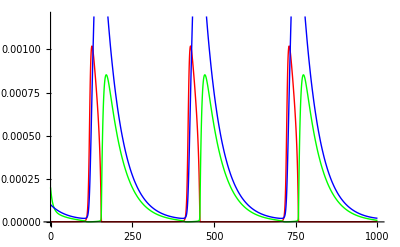

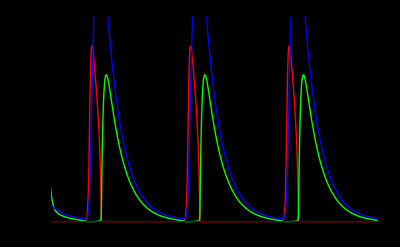

```mathematica
intX =Interpolation[Table[{t[i], X[i]}, {i, 0, tmax-1}]];
intY =Interpolation[Table[{t[i], Y[i]}, {i, 0, tmax-1}]];
intZ =Interpolation[Table[{t[i], Z[i]}, {i, 0, tmax-1}]];
Plot[Evaluate[{10*intX[t], 10*intY[t], intZ[t]}], {t, 0, 1000},
         PlotStyle->{{Red, Thick}, {Green, Thick}, {Blue, Thick}}]

Plot[Evaluate[{10*intX[t], 10*intY[t], intZ[t]}], {t, 0, 1000},
   PlotStyle->{{Red, Thick}, {Green, Thick}, {Blue, Thick}},AxesStyle->Directive[White, 14], Background->Black]
```

A 3D plot allows for direct visualization of the orbits.

```mathematica
intF=Interpolation[Table[{{t},{X[t],Y[t],Z[t]}},{t,0,tmax}]];
options={PlotStyle->{Orange,Specularity[White,10],Tube[.0000005]},Background->Black,Boxed->False,Axes->False,PlotRange->All,BoxRatios->1};
ParametricPlot3D[intF[t],{t,0,tmax},Evaluate@options]
```

-Graphics3D-